```mathematica
(*Mathematica*)
```

```mathematica
(* bezier Mandelbrot Julia: as a Julia set on complex plane c point*)
```

```mathematica
Clear[f,g0,g,v]
```

```mathematica
f[z_,i_]=z^2+(0.1414234708212833+0.5836690226625129 ⅈ)*(i/30)+(1-i/30)*(0.14286182869214717+0.5825691396525865 ⅈ)
```

(0.142862+0.582569 ⅈ) (1-i/30)+(0.00471412+0.0194556 ⅈ) i+z^2

```mathematica
(*{6.,48.683432},{31.,47.85921}*)
```

```mathematica
f[z,6]
```

(0.142574+0.582789 ⅈ)+z^2

```mathematica
Norm[0.1425741571179744+0.5827891162545717 ⅈ]
```

0.599975

```mathematica
g1=Flatten[ParallelTable[{i,Timing[JuliaSetPlot[f[z,i],z,Method -> "OrbitDetection",ColorFunction->Hue,ImageSize->{1920,1080},PlotStyle->{Opacity[0.2],Red,PointSize[0.0005]},AspectRatio->1,ImageResolution->1920,PerformanceGoal->"Quality","Bound"->32,Frame->False,Axes->False]][[1]]},{i,-40,70}]];
```

```mathematica
Length[g1]
```

222

```mathematica
g1
```

{-40,38.1531,-39,40.8452,-38,45.6729,-37,43.7538,-36,43.5634,-35,37.7398,-34,37.6553,-33,37.6954,-32,40.8052,-31,43.1351,-30,43.5659,-29,41.0172,-28,41.9895,-27,42.7215,-26,35.5484,-25,39.5719,-24,39.6891,-23,37.2815,-22,46.6993,-21,40.6436,-20,40.2088,-19,40.9792,-18,41.8417,-17,37.6164,-16,35.2761,-15,36.7981,-14,34.8826,-13,37.7196,-12,41.234,-11,42.0041,-10,43.0205,-9,45.5169,-8,38.1,-7,46.8198,-6,43.6831,-5,36.0347,-4,35.9411,-3,36.9214,-2,39.3495,-1,43.373,0,44.2994,1,45.9605,2,42.2524,3,44.9586,4,45.9714,5,45.656,6,48.6834,7,42.8995,8,40.524,9,43.5025,10,45.1931,11,46.081,12,43.3963,13,37.7576,14,40.847,15,42.1482,16,42.2078,17,41.0369,18,45.0599,19,42.8639,20,44.1142,21,43.5718,22,44.7474,23,45.1392,24,43.1815,25,41.044,26,43.1244,27,37.7725,28,39.0417,29,43.751,30,45.7519,31,47.8592,32,40.2746,33,37.3829,34,40.4612,35,40.5525,36,43.5183,37,42.2868,38,40.1109,39,35.8789,40,38.3398,41,36.0946,42,45.0081,43,36.7663,44,40.7759,45,36.4446,46,40.9731,47,40.0661,48,35.4944,49,38.5233,50,38.3432,51,39.6598,52,36.399,53,41.7824,54,39.0068,55,39.0192,56,41.3599,57,40.9186,58,38.3027,59,39.286,60,36.3865,61,35.5772,62,37.0864,63,36.4284,64,42.4391,65,44.3279,66,39.3404,67,39.2062,68,41.3403,69,39.2238,70,38.1501}

```mathematica
gg=Table[N[{g1[[i]],g1[[i+1]]}],{i,1,Length[g1]-1,2}]
```

{{-40.,38.1531},{-39.,40.8452},{-38.,45.6729},{-37.,43.7538},{-36.,43.5634},{-35.,37.7398},{-34.,37.6553},{-33.,37.6954},{-32.,40.8052},{-31.,43.1351},{-30.,43.5659},{-29.,41.0172},{-28.,41.9895},{-27.,42.7215},{-26.,35.5484},{-25.,39.5719},{-24.,39.6891},{-23.,37.2815},{-22.,46.6993},{-21.,40.6436},{-20.,40.2088},{-19.,40.9792},{-18.,41.8417},{-17.,37.6164},{-16.,35.2761},{-15.,36.7981},{-14.,34.8826},{-13.,37.7196},{-12.,41.234},{-11.,42.0041},{-10.,43.0205},{-9.,45.5169},{-8.,38.1},{-7.,46.8198},{-6.,43.6831},{-5.,36.0347},{-4.,35.9411},{-3.,36.9214},{-2.,39.3495},{-1.,43.373},{0.,44.2994},{1.,45.9605},{2.,42.2524},{3.,44.9586},{4.,45.9714},{5.,45.656},{6.,48.6834},{7.,42.8995},{8.,40.524},{9.,43.5025},{10.,45.1931},{11.,46.081},{12.,43.3963},{13.,37.7576},{14.,40.847},{15.,42.1482},{16.,42.2078},{17.,41.0369},{18.,45.0599},{19.,42.8639},{20.,44.1142},{21.,43.5718},{22.,44.7474},{23.,45.1392},{24.,43.1815},{25.,41.044},{26.,43.1244},{27.,37.7725},{28.,39.0417},{29.,43.751},{30.,45.7519},{31.,47.8592},{32.,40.2746},{33.,37.3829},{34.,40.4612},{35.,40.5525},{36.,43.5183},{37.,42.2868},{38.,40.1109},{39.,35.8789},{40.,38.3398},{41.,36.0946},{42.,45.0081},{43.,36.7663},{44.,40.7759},{45.,36.4446},{46.,40.9731},{47.,40.0661},{48.,35.4944},{49.,38.5233},{50.,38.3432},{51.,39.6598},{52.,36.399},{53.,41.7824},{54.,39.0068},{55.,39.0192},{56.,41.3599},{57.,40.9186},{58.,38.3027},{59.,39.286},{60.,36.3865},{61.,35.5772},{62.,37.0864},{63.,36.4284},{64.,42.4391},{65.,44.3279},{66.,39.3404},{67.,39.2062},{68.,41.3403},{69.,39.2238},{70.,38.1501}}

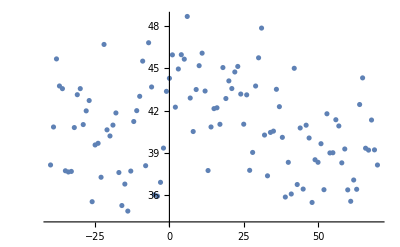

```mathematica
ListPlot[gg]
```

```mathematica
(*end*)
```